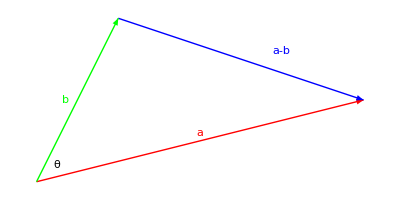

```mathematica
Graphics[{
Thick, Style[Text[θ, {.25,.2}], 18],Red, Style[Text[a, {2,.6}], 18],Arrow[{{0,0}, {4,1}}], Green, Style[Text[b, {.35,1}], 18],Arrow[{{0,0}, {1,2}}], Blue, Style[Text[a-b, {3,1.6}], 18],Arrow[{{1,2}, {4,1}}]
}]
```

```mathematica
Graphics3D[{
AxesOrigin->{0,0,0}, Red, Thick, Arrow[{{0,0,0}, {2,0,4}}], Green, Arrow[{{0,0,0}, {-1,1,2}}], Blue, Arrow[{{0,0,0}, {-4,-8,2}}]
}]
```

-Graphics3D-

```mathematica
{2,0,4}×{-1,1,2}
```

{-4,-8,2}

```mathematica
Graphics[
{
Thick, Red, Arrow[{{0,0}, {6,3}}], Blue, Arrow[{{0,0}, {3,4}}], Opacity[0.8],Green, Arrow[{{0,0},{4,2}}],Black,Dashed, Line[{{3,4},{4, 2}}]
}
]
```

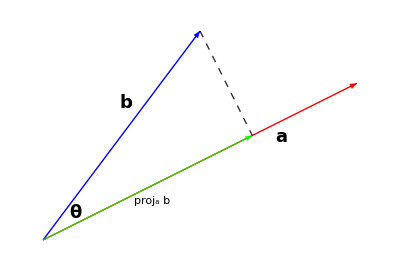

```mathematica
Graphics3D[
{
Text[θ, {0.1, 0, 0.4}],Text[h, {.45, .25, .5}],BezierCurve[{{0,0,0.5},{.125,.125,.625},{.25,.25,0.5}}],Opacity[0.5],EdgeForm[Thin],Parallelepiped[{0,0,0},{{2,0,0}, {1,1,0},{.5,.5,1}}],Opacity[1], {Dashed, Line[{{0,0,1},{.5, .5, 1}, {.5, .5, 0}}]},
Thick, Red, Arrow[{{0,0,0}, {2,0,0}}], Text[a, {1,0,0.1}],Green, Text[b, {0.5, 0.5, 0.1}],Arrow[{{0,0,0}, {1,1,0}}], Blue, Text[c, {.25, .25, 0.7}],Arrow[{{0,0,0}, {.5,.5,1}}], Purple, Text[b×c, {0.15,0,1}],Arrow[{{0,0,0},{0,0,2}}]
}, Boxed->False]
```

-Graphics3D-

```mathematica
r[t_]:={3, -2, -1} + t{-2,5,2};
Graphics3D[
{
PointSize[Large],Orange, Line[{r[0.3], r[1]}],
Thick, Red, Arrow[{{0,0,0}, r[.60]}], Point[r[.6]],Text[Subscript[P, 0],(r[.6]+{0.1,0.1,0.2})],Green, Arrow[{{0,0,0}, r[0.9]}],Point[r[.9]],Text[P,(r[.9]+{0.1,0.1,0.2})],
Purple, Arrow[{r[0.6], r[0.9]}], Blue, Arrow[{{0,0,0}, 0.2{-2,5,2}}], Text[v, 0.22{-2,5,2}]
}, Boxed->False, Axes->True, AxesOrigin->{0,0,0}, Ticks->None, AxesLabel->{x,y,z}
]
```

-Graphics3D-